```mathematica
β[ω_,δ_,t_,ϵ_]:=
β[ω,δ,t,ϵ]=ReplacePart[(ω+ⅈ*δ-ϵ)IdentityMatrix[14],Join[Table[{i,i-1},{i,Range[2,14,1]}],Table[{i,i+1},{i,Range[1,14,1]}],Table[{2n-1,14-2n+2},{n,4}],Table[{14-2n+2,2n-1},{n,3}]]->-t]
```

```mathematica
T1[t_]:=T1[t]=ReplacePart[0*IdentityMatrix[14],Table[{2n,14-2n+1},{n,3}]->t]
```

```mathematica
TT[t_]:=ReplacePart[0*IdentityMatrix[14],Table[{2n,2n},{n,3}]->t]
```

```mathematica
LEFT[ω_,δ_,t_,ϵ_]:=LEFT[ω,δ,t,ϵ]=Module[{J=Inverse[β[ω,0.0001,1,0]],B:=Inverse[β[ω,0.0001,1,0]],T1:=T1[1]},Do[J=Inverse[IdentityMatrix[14]-B.ConjugateTranspose[T1].J.T1].B,8000]; J=J]
```

```mathematica
g[ω_,δ_,t_,ϵ_]:= Inverse[β[ω,δ,t,ϵ]]
```

```mathematica
SR[ω_,δ_,t_,ϵ_]:=SR[ω,δ,t,ϵ]=Inverse[IdentityMatrix[14]-g[ω,δ,t,ϵ].ConjugateTranspose[T1[t]].LEFT[ω,δ,t,ϵ].T1[t]].g[ω,δ,t,ϵ]
```

```mathematica
SL[ω_,δ_,t_,ϵ_]:=SL[ω,δ,t,ϵ]=Inverse[IdentityMatrix[14]-g[ω,δ,t,ϵ].ConjugateTranspose[T1[t]].LEFT[ω,δ,t,ϵ].T1[t]].g[ω,δ,t,ϵ]
```

```mathematica
IL[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[14]-SL[ω,δ,t,ϵ].TT[t].SR[ω,δ,t,ϵ].TT[t]].SL[ω,δ,t,ϵ]
```

```mathematica
IR[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[14]-SR[ω,δ,t,ϵ].TT[t].SL[ω,δ,t,ϵ].TT[t]].SR[ω,δ,t,ϵ]
```

```mathematica
gdd[ω_,δ_,t_,ϵ_]:= IL[ω,δ,t,ϵ]-ConjugateTranspose[IL[ω,δ,t,ϵ]]
```

```mathematica
grr[ω_,δ_,t_,ϵ_]:= IR[ω,δ,t,ϵ]-ConjugateTranspose[IR[ω,δ,t,ϵ]]
```

```mathematica
Gnonlocal[ω_,δ_,t_,ϵ_]:= SR[ω,δ,t,ϵ].TT[t].IL[ω,δ,t,ϵ]
```

```mathematica
GNON[ω_,δ_,t_,ϵ_]:= Gnonlocal[ω,δ,t,ϵ]-ConjugateTranspose[Gnonlocal[ω,δ,t,ϵ]]
```

```mathematica
tr[ω_,δ_,t_,ϵ_]:= Abs[Tr[gdd[ω,δ,t,ϵ].TT[t].grr[ω,δ,t,ϵ].TT[t]-TT[t].GNON[ω,δ,t,ϵ].TT[t].GNON[ω,δ,t,ϵ]]]
```

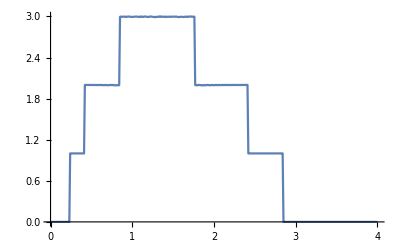

```mathematica
ListLinePlot[Table[{ω,tr[ω,0.0001,1,0]},{ω,0,4,0.01}]]
```

```mathematica
pris=Table[{ω,tr[ω,0.0001,1,0]},{ω,0,4,0.01}]
```

{{0.,2.8×10^-7},{0.01,2.8081×10^-7},{0.02,2.83264×10^-7},{0.03,2.87439×10^-7},{0.04,2.93463×10^-7},{0.05,3.01536×10^-7},{0.06,3.11935×10^-7},{0.07,3.25045×10^-7},{0.08,3.41391×10^-7},{0.09,3.61694×10^-7},{0.1,3.86954×10^-7},{0.11,4.18578×10^-7},{0.12,4.58598×10^-7},{0.13,5.10023×10^-7},{0.14,5.77474×10^-7},{0.15,6.68349×10^-7},{0.16,7.95126×10^-7},{0.17,9.803×10^-7},{0.18,1.26801×10^-6},{0.19,1.75544×10^-6},{0.2,2.69447×10^-6},{0.21,4.92698×10^-6},{0.22,0.0000129427},{0.23,0.000120119},{0.24,0.999916},{0.25,0.999991},{0.26,0.999998},{0.27,1.},{0.28,0.999998},{0.29,0.999999},{0.3,0.999999},{0.31,0.999946},{0.32,0.999915},{0.33,0.999952},{0.34,0.999996},{0.35,0.999822},{0.36,0.999769},{0.37,0.999735},{0.38,1.},{0.39,0.999893},{0.4,0.99963},{0.41,1.00011},{0.42,1.99987},{0.43,1.99945},{0.44,1.99999},{0.45,1.99952},{0.46,1.99971},{0.47,1.99943},{0.48,1.99973},{0.49,1.99925},{0.5,1.99995},{0.51,1.99998},{0.52,1.99872},{0.53,1.99903},{0.54,1.99915},{0.55,1.99899},{0.56,1.99923},{0.57,1.99871},{0.58,1.9985},{0.59,1.99935},{0.6,1.9983},{0.61,1.99973},{0.62,1.99964},{0.63,1.99728},{0.64,1.99869},{0.65,1.99639},{0.66,1.99654},{0.67,1.99915},{0.68,1.99865},{0.69,1.99668},{0.7,1.99573},{0.71,1.99501},{0.72,1.99995},{0.73,1.99796},{0.74,1.99942},{0.75,1.99859},{0.76,1.99888},{0.77,1.99973},{0.78,1.99422},{0.79,1.99392},{0.8,1.99748},{0.81,1.99466},{0.82,1.99673},{0.83,1.99427},{0.84,1.99729},{0.85,2.99415},{0.86,2.99738},{0.87,2.9969},{0.88,2.99368},{0.89,2.99688},{0.9,2.99703},{0.91,2.99826},{0.92,2.99306},{0.93,2.99479},{0.94,2.99702},{0.95,2.99795},{0.96,2.99838},{0.97,2.99731},{0.98,2.99533},{0.99,2.99384},{1.,2.99292},{1.01,2.99364},{1.02,2.99578},{1.03,2.99662},{1.04,2.99781},{1.05,2.99861},{1.06,2.99696},{1.07,2.99589},{1.08,2.99219},{1.09,2.9932},{1.1,2.99975},{1.11,2.99456},{1.12,2.99765},{1.13,2.99223},{1.14,2.99549},{1.15,2.99935},{1.16,2.99916},{1.17,2.99604},{1.18,2.99491},{1.19,2.99388},{1.2,2.99225},{1.21,2.99619},{1.22,2.99985},{1.23,2.99859},{1.24,2.99607},{1.25,2.99439},{1.26,2.99278},{1.27,2.99171},{1.28,2.99009},{1.29,2.99517},{1.3,2.99131},{1.31,2.99452},{1.32,2.99871},{1.33,2.99407},{1.34,2.99995},{1.35,2.99374},{1.36,2.99898},{1.37,2.99554},{1.38,2.99573},{1.39,2.99695},{1.4,2.991},{1.41,2.99716},{1.42,2.99663},{1.43,2.99259},{1.44,2.99574},{1.45,2.99645},{1.46,2.99659},{1.47,2.99298},{1.48,2.99688},{1.49,2.99598},{1.5,2.99759},{1.51,2.99686},{1.52,2.99775},{1.53,2.99612},{1.54,2.99757},{1.55,2.99537},{1.56,2.99078},{1.57,2.99069},{1.58,2.99396},{1.59,2.99454},{1.6,2.99467},{1.61,2.99472},{1.62,2.9927},{1.63,2.9921},{1.64,2.99471},{1.65,2.99782},{1.66,2.99345},{1.67,2.99714},{1.68,2.9918},{1.69,2.99801},{1.7,2.99855},{1.71,2.9991},{1.72,2.9991},{1.73,2.99487},{1.74,2.9974},{1.75,2.99466},{1.76,2.99766},{1.77,1.99834},{1.78,1.99608},{1.79,1.99395},{1.8,1.99764},{1.81,1.99978},{1.82,1.99923},{1.83,1.99669},{1.84,1.99756},{1.85,1.99419},{1.86,1.99449},{1.87,1.99911},{1.88,1.99467},{1.89,1.99628},{1.9,1.99475},{1.91,1.99973},{1.92,1.99872},{1.93,1.99955},{1.94,1.99567},{1.95,1.99658},{1.96,1.99597},{1.97,1.99901},{1.98,1.99937},{1.99,1.99601},{2.,1.9979},{2.01,1.99629},{2.02,1.99987},{2.03,1.99932},{2.04,1.99719},{2.05,1.99723},{2.06,1.99969},{2.07,1.99981},{2.08,1.99704},{2.09,1.9971},{2.1,1.99995},{2.11,1.99965},{2.12,1.99871},{2.13,1.99995},{2.14,1.99908},{2.15,1.99907},{2.16,1.99869},{2.17,1.99998},{2.18,1.99832},{2.19,1.99819},{2.2,1.99945},{2.21,1.9987},{2.22,1.99985},{2.23,1.99987},{2.24,1.99901},{2.25,1.99902},{2.26,1.99933},{2.27,1.99996},{2.28,1.99936},{2.29,1.99901},{2.3,1.99895},{2.31,1.99899},{2.32,1.99904},{2.33,1.99916},{2.34,1.99957},{2.35,2.},{2.36,1.9993},{2.37,1.99999},{2.38,1.99988},{2.39,1.99998},{2.4,1.99953},{2.41,1.99974},{2.42,0.999707},{2.43,1.},{2.44,0.999808},{2.45,0.999992},{2.46,0.99971},{2.47,0.999831},{2.48,0.999838},{2.49,0.999799},{2.5,0.999848},{2.51,0.999922},{2.52,0.99992},{2.53,0.999886},{2.54,0.999958},{2.55,0.999932},{2.56,0.999992},{2.57,0.999952},{2.58,0.999996},{2.59,0.999968},{2.6,0.999968},{2.61,0.999988},{2.62,0.999995},{2.63,0.999995},{2.64,0.999997},{2.65,1.},{2.66,0.999996},{2.67,1.},{2.68,0.999999},{2.69,1.},{2.7,0.999998},{2.71,1.},{2.72,1.},{2.73,0.999999},{2.74,1.},{2.75,1.},{2.76,1.},{2.77,1.},{2.78,0.999999},{2.79,0.999999},{2.8,0.999999},{2.81,0.999998},{2.82,0.999997},{2.83,0.999992},{2.84,0.999958},{2.85,0.000496198},{2.86,0.0000165305},{2.87,4.97473×10^-6},{2.88,2.35363×10^-6},{2.89,1.36412×10^-6},{2.9,8.87821×10^-7},{2.91,6.22951×10^-7},{2.92,4.6079×10^-7},{2.93,3.54437×10^-7},{2.94,2.8098×10^-7},{2.95,2.28152×10^-7},{2.96,1.88907×10^-7},{2.97,1.58966×10^-7},{2.98,1.35611×10^-7},{2.99,1.17044×10^-7},{3.,1.02043×10^-7},{3.01,8.97514×10^-8},{3.02,7.9554×10^-8},{3.03,7.10012×10^-8},{3.04,6.37576×10^-8},{3.05,5.75691×10^-8},{3.06,5.22402×10^-8},{3.07,4.76186×10^-8},{3.08,4.35846×10^-8},{3.09,4.00423×10^-8},{3.1,3.69149×10^-8},{3.11,3.414×10^-8},{3.12,3.16663×10^-8},{3.13,2.94518×10^-8},{3.14,2.74614×10^-8},{3.15,2.56657×10^-8},{3.16,2.40401×10^-8},{3.17,2.25637×10^-8},{3.18,2.12187×10^-8},{3.19,1.99899×10^-8},{3.2,1.88644×10^-8},{3.21,1.78307×10^-8},{3.22,1.68791×10^-8},{3.23,1.60012×10^-8},{3.24,1.51895×10^-8},{3.25,1.44374×10^-8},{3.26,1.37393×10^-8},{3.27,1.30901×10^-8},{3.28,1.24853×10^-8},{3.29,1.1921×10^-8},{3.3,1.13935×10^-8},{3.31,1.08998×10^-8},{3.32,1.0437×10^-8},{3.33,1.00026×10^-8},{3.34,9.59432×10^-9},{3.35,9.21007×10^-9},{3.36,8.84801×10^-9},{3.37,8.50646×10^-9},{3.38,8.1839×10^-9},{3.39,7.87895×10^-9},{3.4,7.59034×10^-9},{3.41,7.31692×10^-9},{3.42,7.05766×10^-9},{3.43,6.81158×10^-9},{3.44,6.5778×10^-9},{3.45,6.35553×10^-9},{3.46,6.14401×10^-9},{3.47,5.94257×10^-9},{3.48,5.75058×10^-9},{3.49,5.56745×10^-9},{3.5,5.39265×10^-9},{3.51,5.22569×10^-9},{3.52,5.06609×10^-9},{3.53,4.91344×10^-9},{3.54,4.76734×10^-9},{3.55,4.62743×10^-9},{3.56,4.49335×10^-9},{3.57,4.36479×10^-9},{3.58,4.24145×10^-9},{3.59,4.12306×10^-9},{3.6,4.00935×10^-9},{3.61,3.90008×10^-9},{3.62,3.79503×10^-9},{3.63,3.69399×10^-9},{3.64,3.59674×10^-9},{3.65,3.50311×10^-9},{3.66,3.41293×10^-9},{3.67,3.32601×10^-9},{3.68,3.24222×10^-9},{3.69,3.1614×10^-9},{3.7,3.08341×10^-9},{3.71,3.00813×10^-9},{3.72,2.93544×10^-9},{3.73,2.86521×10^-9},{3.74,2.79734×10^-9},{3.75,2.73172×10^-9},{3.76,2.66827×10^-9},{3.77,2.60687×10^-9},{3.78,2.54746×10^-9},{3.79,2.48994×10^-9},{3.8,2.43423×10^-9},{3.81,2.38026×10^-9},{3.82,2.32797×10^-9},{3.83,2.27728×10^-9},{3.84,2.22812×10^-9},{3.85,2.18045×10^-9},{3.86,2.13419×10^-9},{3.87,2.08931×10^-9},{3.88,2.04573×10^-9},{3.89,2.00342×10^-9},{3.9,1.96232×10^-9},{3.91,1.92239×10^-9},{3.92,1.88359×10^-9},{3.93,1.84588×10^-9},{3.94,1.80921×10^-9},{3.95,1.77355×10^-9},{3.96,1.73887×10^-9},{3.97,1.70512×10^-9},{3.98,1.67227×10^-9},{3.99,1.64031×10^-9},{4.,1.60918×10^-9}}

```mathematica
RandomSample[Join[RandomSample[{imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,imp9,imp10,imp11,imp12,imp14,imp13},7],RandomSample[{imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,imp9,imp10,imp11,imp12,imp14,imp13}],(*RandomSample[{imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,imp9,imp10,imp11,imp12,imp14,imp13}],RandomSample[{imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,imp9,imp10,imp11,imp12,imp14,imp13}],RandomSample[{imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,imp9,imp10,imp11,imp12,imp14,imp13}],RandomSample[{imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,imp9,imp10,imp11,imp12,imp14,imp13}],*)Table[imp,29]]]
```

{imp,imp,imp,imp,imp,imp,imp5,imp,imp9,imp5,imp1,imp6,imp13,imp,imp,imp,imp,imp3,imp,imp13,imp12,imp11,imp2,imp,imp7,imp9,imp,imp,imp4,imp,imp,imp12,imp,imp14,imp8,imp11,imp8,imp,imp2,imp,imp,imp,imp,imp,imp,imp10,imp,imp,imp,imp}

```mathematica
m3[ω_,ϵ1_]:=Module[{Tin=T1[1],T=TT[1],,μ1=RandomInteger[{1,14}], μ2=RandomInteger[{1,14}], μ3=RandomInteger[{1,14}], μ4=RandomInteger[{1,14}],μ5=RandomInteger[{1,14}], μ6=RandomInteger[{1,14}], μ7=RandomInteger[{1,14}],μ8=RandomInteger[{1,14}], μ9=RandomInteger[{1,14}], μ10=RandomInteger[{1,14}], μ11=RandomInteger[{1,14}],μ12=RandomInteger[{1,14}], μ13=RandomInteger[{1,14}], μ14=RandomInteger[{1,14}], μ15=RandomInteger[{8,14}],μ16=RandomInteger[{8,14}]},
tra1:=Module[{},
b=Module[{imp1:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ1,μ1}}->ω+ⅈ*0.0001-ϵ1]]],
imp2:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ2,μ2}}->ω+ⅈ*0.0001-ϵ1]]],
imp3:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ3,μ3}}->ω+ⅈ*0.0001-ϵ1]]],
imp4:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ4,μ4}}->ω+ⅈ*0.0001-ϵ1]]],
imp5:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ5,μ5}}->ω+ⅈ*0.0001-ϵ1]]],
imp6:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ6,μ6}}->ω+ⅈ*0.0001-ϵ1]]],
imp7:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ7,μ7}}->ω+ⅈ*0.0001-ϵ1]]],
imp8:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ8,μ8}}->ω+ⅈ*0.0001-ϵ1]]],
imp9:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ9,μ9}}->ω+ⅈ*0.0001-ϵ1]]],
imp10:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ10,μ10}}->ω+ⅈ*0.0001-ϵ1]]],
imp11:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ11,μ11}}->ω+ⅈ*0.0001-ϵ1]]],
imp12:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ12,μ12}}->ω+ⅈ*0.0001-ϵ1]]],
imp13:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ13,μ13}}->ω+ⅈ*0.0001-ϵ1]]],
imp14:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ14,μ14}}->ω+ⅈ*0.0001-ϵ1]]],
imp:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{14,14}}->ω+ⅈ*0.0001-0]]]},
lista={RandomSample[{imp,imp,imp9,imp,imp12,imp,imp7,imp,imp,imp13,imp8,imp,imp12,imp,imp,imp,imp,imp,imp3,imp2,imp,imp,imp,imp,imp14,imp6,imp,imp10,imp,imp11,imp2,imp4,imp,imp,imp,imp,imp13,imp,imp,imp,imp11,imp,imp5,imp,imp,imp14,imp5,imp6,imp,imp1}]};
sl1= Module[{J=SL[ω,0.0001,1,0]},Do[J=Inverse[IdentityMatrix[14]-lista[[1,ζ]].ConjugateTranspose[Tin].J.Tin].lista[[1,ζ]],{ζ,1,50}];J=J];Il1:=Inverse[IdentityMatrix[14]-sl1.T.SR[ω,0.0001,1,0].T].sl1;
Ir1:=Inverse[IdentityMatrix[14]-SR[ω,0.0001,1,0].T.sl1.T].SR[ω,0.0001,1,0];gdd1:= Il1-ConjugateTranspose[Il1];grr1:= Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SR[ω,0.0001,1,0].T.Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];If[Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]>pris[[ω*100+1]][[2]],pris[[ω*100+1]][[2]],Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]]];
b];
tra1]
```

```mathematica
f[M_]:=Table[{ω,Mean[Table[m3[ω,0.5],M]]},{ω,Range[0,1.5,0.01]}]
```

```mathematica
f[50]
```

{{0.,2.68917×10^-7},{0.01,2.50025×10^-7},{0.02,2.54219×10^-7},{0.03,2.54116×10^-7},{0.04,2.63025×10^-7},{0.05,2.87135×10^-7},{0.06,2.98465×10^-7},{0.07,3.01316×10^-7},{0.08,3.13976×10^-7},{0.09,3.57135×10^-7},{0.1,3.64819×10^-7},{0.11,3.96976×10^-7},{0.12,4.49922×10^-7},{0.13,4.71035×10^-7},{0.14,5.55455×10^-7},{0.15,6.55435×10^-7},{0.16,7.38562×10^-7},{0.17,9.68342×10^-7},{0.18,1.21681×10^-6},{0.19,1.68912×10^-6},{0.2,2.55023×10^-6},{0.21,4.77777×10^-6},{0.22,0.0000124566},{0.23,0.000110354},{0.24,0.0819371},{0.25,0.221329},{0.26,0.369987},{0.27,0.564757},{0.28,0.624639},{0.29,0.64984},{0.3,0.686192},{0.31,0.758923},{0.32,0.760358},{0.33,0.77582},{0.34,0.829238},{0.35,0.769856},{0.36,0.746467},{0.37,0.766098},{0.38,0.769028},{0.39,0.802235},{0.4,0.724324},{0.41,0.605141},{0.42,0.610767},{0.43,0.821745},{0.44,0.631051},{0.45,0.742359},{0.46,1.04746},{0.47,1.00124},{0.48,1.12489},{0.49,1.08445},{0.5,1.26229},{0.51,1.29976},{0.52,1.28811},{0.53,1.37497},{0.54,1.37783},{0.55,1.36236},{0.56,1.49789},{0.57,1.38279},{0.58,1.42955},{0.59,1.41613},{0.6,1.47494},{0.61,1.49547},{0.62,1.45602},{0.63,1.43291},{0.64,1.47591},{0.65,1.48041},{0.66,1.55911},{0.67,1.56565},{0.68,1.52651},{0.69,1.60643},{0.7,1.59316},{0.71,1.53416},{0.72,1.53545},{0.73,1.55362},{0.74,1.51412},{0.75,1.55682},{0.76,1.58431},{0.77,1.53704},{0.78,1.57704},{0.79,1.5576},{0.8,1.59292},{0.81,1.65374},{0.82,1.64253},{0.83,1.62653},{0.84,1.55437},{0.85,0.976547},{0.86,0.911768},{0.87,0.938724},{0.88,1.16694},{0.89,1.29962},{0.9,1.47485},{0.91,1.54789},{0.92,1.65995},{0.93,1.82571},{0.94,2.00735},{0.95,1.90904},{0.96,2.024},{0.97,2.14793},{0.98,1.99273},{0.99,2.02363},{1.,2.1362},{1.01,2.22572},{1.02,2.1234},{1.03,1.83654},{1.04,1.34369},{1.05,0.662107},{1.06,0.336484},{1.07,0.336675},{1.08,0.425921},{1.09,0.636695},{1.1,0.837808},{1.11,0.899881},{1.12,1.07653},{1.13,1.30519},{1.14,1.2701},{1.15,1.43212},{1.16,1.41709},{1.17,1.5166},{1.18,1.52716},{1.19,1.67193},{1.2,1.52348},{1.21,1.67224},{1.22,1.66089},{1.23,1.61814},{1.24,1.62744},{1.25,1.67006},{1.26,1.59395},{1.27,1.66293},{1.28,1.68131},{1.29,1.56602},{1.3,1.68284},{1.31,1.70251},{1.32,1.631},{1.33,1.72013},{1.34,1.64439},{1.35,1.70243},{1.36,1.72528},{1.37,1.67818},{1.38,1.68633},{1.39,1.74775},{1.4,1.74667},{1.41,1.72974},{1.42,1.65417},{1.43,1.55713},{1.44,1.7207},{1.45,1.68958},{1.46,1.52825},{1.47,1.66265},{1.48,1.60861},{1.49,1.60869},{1.5,1.52489}}

```mathematica
Export["/home/shardulmukim/PhD/fwi/7AGNR/50unitcells/errorm3/m50.dat",%20]
Export["/home/shardulmukim/PhD/fwi/7AGNR/50unitcells/errorm3/m100.dat",%21]
Export["/home/shardulmukim/PhD/fwi/7AGNR/50unitcells/errorm3/m200.dat",%22]
Export["/home/shardulmukim/PhD/fwi/7AGNR/50unitcells/errorm3/m400.dat",%23]
Export["/home/shardulmukim/PhD/fwi/7AGNR/50unitcells/errorm3/m800.dat",%24]
Export["/home/shardulmukim/PhD/fwi/7AGNR/50unitcells/errorm3/m1600.dat",%24]
Export["/home/shardulmukim/PhD/fwi/7AGNR/50unitcells/errorm3/m1600.dat",%25]
```

/home/shardulmukim/PhD/fwi/7AGNR/50unitcells/errorm3/m50.dat

/home/shardulmukim/PhD/fwi/7AGNR/50unitcells/errorm3/m100.dat

/home/shardulmukim/PhD/fwi/7AGNR/50unitcells/errorm3/m200.dat

/home/shardulmukim/PhD/fwi/7AGNR/50unitcells/errorm3/m400.dat

/home/shardulmukim/PhD/fwi/7AGNR/50unitcells/errorm3/m800.dat

/home/shardulmukim/PhD/fwi/7AGNR/50unitcells/errorm3/m1600.dat

/home/shardulmukim/PhD/fwi/7AGNR/50unitcells/errorm3/m1600.dat

```mathematica
f[100]
```

{{0.,2.60983×10^-7},{0.01,2.20877×10^-7},{0.02,2.53525×10^-7},{0.03,2.61907×10^-7},{0.04,2.77339×10^-7},{0.05,2.82291×10^-7},{0.06,3.02616×10^-7},{0.07,3.00228×10^-7},{0.08,3.16286×10^-7},{0.09,3.4156×10^-7},{0.1,3.67322×10^-7},{0.11,3.88332×10^-7},{0.12,4.32249×10^-7},{0.13,4.93209×10^-7},{0.14,5.59534×10^-7},{0.15,6.12796×10^-7},{0.16,7.5706×10^-7},{0.17,9.2464×10^-7},{0.18,1.20084×10^-6},{0.19,1.67553×10^-6},{0.2,2.62004×10^-6},{0.21,4.60479×10^-6},{0.22,0.0000121734},{0.23,0.000110862},{0.24,0.0807793},{0.25,0.171991},{0.26,0.488204},{0.27,0.592214},{0.28,0.630453},{0.29,0.639859},{0.3,0.711418},{0.31,0.737126},{0.32,0.773207},{0.33,0.761144},{0.34,0.766989},{0.35,0.764479},{0.36,0.771387},{0.37,0.782971},{0.38,0.80174},{0.39,0.735228},{0.4,0.725401},{0.41,0.636461},{0.42,0.580983},{0.43,0.72316},{0.44,0.721174},{0.45,0.782984},{0.46,0.984249},{0.47,0.952222},{0.48,1.19554},{0.49,1.18445},{0.5,1.27146},{0.51,1.29532},{0.52,1.21887},{0.53,1.26825},{0.54,1.29577},{0.55,1.44084},{0.56,1.37874},{0.57,1.45019},{0.58,1.43425},{0.59,1.47526},{0.6,1.4802},{0.61,1.4708},{0.62,1.45846},{0.63,1.47238},{0.64,1.52797},{0.65,1.53577},{0.66,1.53898},{0.67,1.53461},{0.68,1.53255},{0.69,1.52998},{0.7,1.57394},{0.71,1.53593},{0.72,1.53243},{0.73,1.58602},{0.74,1.56718},{0.75,1.58187},{0.76,1.59968},{0.77,1.57772},{0.78,1.562},{0.79,1.61044},{0.8,1.60779},{0.81,1.58065},{0.82,1.6144},{0.83,1.54554},{0.84,1.5328},{0.85,0.959435},{0.86,0.891935},{0.87,0.931958},{0.88,1.06977},{0.89,1.26953},{0.9,1.42298},{0.91,1.60048},{0.92,1.66121},{0.93,1.8076},{0.94,1.83509},{0.95,1.93854},{0.96,1.96629},{0.97,2.01721},{0.98,2.04645},{0.99,2.07535},{1.,2.16207},{1.01,2.21075},{1.02,2.15322},{1.03,1.91543},{1.04,1.42744},{1.05,0.578644},{1.06,0.372694},{1.07,0.33543},{1.08,0.423308},{1.09,0.652479},{1.1,0.754515},{1.11,0.990002},{1.12,1.17092},{1.13,1.30262},{1.14,1.31869},{1.15,1.34073},{1.16,1.47536},{1.17,1.46059},{1.18,1.55145},{1.19,1.62103},{1.2,1.61198},{1.21,1.60907},{1.22,1.61133},{1.23,1.67837},{1.24,1.67215},{1.25,1.66785},{1.26,1.65131},{1.27,1.71405},{1.28,1.61901},{1.29,1.5947},{1.3,1.70177},{1.31,1.66644},{1.32,1.68264},{1.33,1.72132},{1.34,1.69132},{1.35,1.67534},{1.36,1.74068},{1.37,1.74232},{1.38,1.70099},{1.39,1.70255},{1.4,1.68421},{1.41,1.62065},{1.42,1.71221},{1.43,1.68062},{1.44,1.6329},{1.45,1.62579},{1.46,1.58299},{1.47,1.63607},{1.48,1.64339},{1.49,1.62813},{1.5,1.60339}}

```mathematica
f[200]
```

{{0.,2.61468×10^-7},{0.01,2.48643×10^-7},{0.02,2.57442×10^-7},{0.03,2.57819×10^-7},{0.04,2.74976×10^-7},{0.05,2.83339×10^-7},{0.06,2.97212×10^-7},{0.07,3.02092×10^-7},{0.08,3.16702×10^-7},{0.09,3.38307×10^-7},{0.1,3.6834×10^-7},{0.11,3.96481×10^-7},{0.12,4.35866×10^-7},{0.13,4.82268×10^-7},{0.14,5.42183×10^-7},{0.15,6.40506×10^-7},{0.16,7.66961×10^-7},{0.17,9.56411×10^-7},{0.18,1.22397×10^-6},{0.19,1.7212×10^-6},{0.2,2.57339×10^-6},{0.21,4.63179×10^-6},{0.22,0.0000122851},{0.23,0.000108316},{0.24,0.0622146},{0.25,0.230581},{0.26,0.47765},{0.27,0.552886},{0.28,0.630893},{0.29,0.651787},{0.3,0.707956},{0.31,0.729243},{0.32,0.766818},{0.33,0.748243},{0.34,0.767224},{0.35,0.776276},{0.36,0.774746},{0.37,0.800222},{0.38,0.784745},{0.39,0.78016},{0.4,0.756223},{0.41,0.649528},{0.42,0.609392},{0.43,0.699249},{0.44,0.817677},{0.45,0.734022},{0.46,0.901861},{0.47,0.97657},{0.48,1.07233},{0.49,1.12955},{0.5,1.20435},{0.51,1.27379},{0.52,1.30187},{0.53,1.27739},{0.54,1.37503},{0.55,1.42051},{0.56,1.44502},{0.57,1.41755},{0.58,1.42239},{0.59,1.44614},{0.6,1.46679},{0.61,1.45853},{0.62,1.49798},{0.63,1.49934},{0.64,1.49816},{0.65,1.51829},{0.66,1.53349},{0.67,1.55758},{0.68,1.55969},{0.69,1.56872},{0.7,1.52197},{0.71,1.53681},{0.72,1.58249},{0.73,1.56739},{0.74,1.58288},{0.75,1.56948},{0.76,1.58062},{0.77,1.56011},{0.78,1.591},{0.79,1.60412},{0.8,1.57826},{0.81,1.58472},{0.82,1.60061},{0.83,1.57791},{0.84,1.50491},{0.85,0.982995},{0.86,0.878071},{0.87,0.942371},{0.88,1.10421},{0.89,1.29475},{0.9,1.39931},{0.91,1.58692},{0.92,1.69015},{0.93,1.80227},{0.94,1.8637},{0.95,1.91586},{0.96,1.96257},{0.97,2.03194},{0.98,2.0599},{0.99,2.17456},{1.,2.19222},{1.01,2.23481},{1.02,2.14159},{1.03,1.93013},{1.04,1.40385},{1.05,0.628786},{1.06,0.30438},{1.07,0.373922},{1.08,0.457466},{1.09,0.595668},{1.1,0.822869},{1.11,1.02641},{1.12,1.1575},{1.13,1.26615},{1.14,1.28963},{1.15,1.35064},{1.16,1.45161},{1.17,1.47586},{1.18,1.54398},{1.19,1.53847},{1.2,1.597},{1.21,1.63394},{1.22,1.65026},{1.23,1.655},{1.24,1.63226},{1.25,1.67916},{1.26,1.6694},{1.27,1.61882},{1.28,1.64015},{1.29,1.66788},{1.3,1.65979},{1.31,1.67907},{1.32,1.68246},{1.33,1.68881},{1.34,1.65165},{1.35,1.70251},{1.36,1.71681},{1.37,1.72819},{1.38,1.68049},{1.39,1.65457},{1.4,1.67005},{1.41,1.68454},{1.42,1.69997},{1.43,1.62827},{1.44,1.68707},{1.45,1.59665},{1.46,1.53707},{1.47,1.61934},{1.48,1.62778},{1.49,1.58093},{1.5,1.63077}}

```mathematica
f[400]
```

{{0.,2.64908×10^-7},{0.01,2.47391×10^-7},{0.02,2.51969×10^-7},{0.03,2.64445×10^-7},{0.04,2.74528×10^-7},{0.05,2.81072×10^-7},{0.06,2.88814×10^-7},{0.07,3.09539×10^-7},{0.08,3.25199×10^-7},{0.09,3.38265×10^-7},{0.1,3.60661×10^-7},{0.11,3.94362×10^-7},{0.12,4.34519×10^-7},{0.13,4.77246×10^-7},{0.14,5.41588×10^-7},{0.15,6.40675×10^-7},{0.16,7.61578×10^-7},{0.17,9.38658×10^-7},{0.18,1.22161×10^-6},{0.19,1.67385×10^-6},{0.2,2.61037×10^-6},{0.21,4.74137×10^-6},{0.22,0.0000121718},{0.23,0.000109348},{0.24,0.0600244},{0.25,0.215999},{0.26,0.441941},{0.27,0.560501},{0.28,0.633958},{0.29,0.693662},{0.3,0.70825},{0.31,0.716027},{0.32,0.753101},{0.33,0.76489},{0.34,0.765246},{0.35,0.771653},{0.36,0.796939},{0.37,0.781827},{0.38,0.781798},{0.39,0.784493},{0.4,0.740655},{0.41,0.651276},{0.42,0.605753},{0.43,0.754327},{0.44,0.71638},{0.45,0.803654},{0.46,0.906349},{0.47,1.01893},{0.48,1.06325},{0.49,1.15722},{0.5,1.21669},{0.51,1.26574},{0.52,1.2884},{0.53,1.35326},{0.54,1.34557},{0.55,1.35948},{0.56,1.3957},{0.57,1.41389},{0.58,1.44051},{0.59,1.44722},{0.6,1.44212},{0.61,1.47827},{0.62,1.50613},{0.63,1.48978},{0.64,1.52502},{0.65,1.51483},{0.66,1.5171},{0.67,1.54241},{0.68,1.53139},{0.69,1.54485},{0.7,1.54088},{0.71,1.54081},{0.72,1.55698},{0.73,1.55745},{0.74,1.57423},{0.75,1.57906},{0.76,1.58902},{0.77,1.56625},{0.78,1.5978},{0.79,1.58627},{0.8,1.60257},{0.81,1.60542},{0.82,1.57794},{0.83,1.56677},{0.84,1.51697},{0.85,1.04294},{0.86,0.912441},{0.87,0.891029},{0.88,1.10371},{0.89,1.26226},{0.9,1.43649},{0.91,1.55916},{0.92,1.69955},{0.93,1.80334},{0.94,1.84449},{0.95,1.90704},{0.96,1.95333},{0.97,2.02089},{0.98,2.08207},{0.99,2.12255},{1.,2.16917},{1.01,2.19249},{1.02,2.13705},{1.03,1.88467},{1.04,1.38628},{1.05,0.637282},{1.06,0.335447},{1.07,0.33702},{1.08,0.407115},{1.09,0.636639},{1.1,0.870088},{1.11,1.01469},{1.12,1.17003},{1.13,1.23549},{1.14,1.34845},{1.15,1.36665},{1.16,1.4246},{1.17,1.48543},{1.18,1.52027},{1.19,1.55262},{1.2,1.58509},{1.21,1.59386},{1.22,1.6507},{1.23,1.68749},{1.24,1.67045},{1.25,1.68032},{1.26,1.6571},{1.27,1.66906},{1.28,1.64598},{1.29,1.67318},{1.3,1.68557},{1.31,1.67979},{1.32,1.69627},{1.33,1.73457},{1.34,1.6903},{1.35,1.6869},{1.36,1.71798},{1.37,1.71939},{1.38,1.72074},{1.39,1.67361},{1.4,1.68938},{1.41,1.71729},{1.42,1.66906},{1.43,1.67666},{1.44,1.6505},{1.45,1.60361},{1.46,1.56817},{1.47,1.59745},{1.48,1.6141},{1.49,1.59703},{1.5,1.60398}}

```mathematica
f[800]
```

{{0.,2.62727×10^-7},{0.01,2.43746×10^-7},{0.02,2.53538×10^-7},{0.03,2.63546×10^-7},{0.04,2.73896×10^-7},{0.05,2.79604×10^-7},{0.06,2.89041×10^-7},{0.07,3.08122×10^-7},{0.08,3.22977×10^-7},{0.09,3.38663×10^-7},{0.1,3.62894×10^-7},{0.11,3.9213×10^-7},{0.12,4.29757×10^-7},{0.13,4.87834×10^-7},{0.14,5.48005×10^-7},{0.15,6.39619×10^-7},{0.16,7.59823×10^-7},{0.17,9.40728×10^-7},{0.18,1.22583×10^-6},{0.19,1.68486×10^-6},{0.2,2.55815×10^-6},{0.21,4.74183×10^-6},{0.22,0.0000122249},{0.23,0.000107348},{0.24,0.0605104},{0.25,0.214608},{0.26,0.444257},{0.27,0.576823},{0.28,0.628748},{0.29,0.660626},{0.3,0.71142},{0.31,0.727999},{0.32,0.748157},{0.33,0.768075},{0.34,0.778734},{0.35,0.788139},{0.36,0.780882},{0.37,0.793061},{0.38,0.786639},{0.39,0.781846},{0.4,0.759658},{0.41,0.659024},{0.42,0.613974},{0.43,0.719391},{0.44,0.700627},{0.45,0.808384},{0.46,0.915302},{0.47,1.02388},{0.48,1.10018},{0.49,1.14604},{0.5,1.22417},{0.51,1.23615},{0.52,1.28426},{0.53,1.33922},{0.54,1.37967},{0.55,1.39252},{0.56,1.37096},{0.57,1.41558},{0.58,1.43561},{0.59,1.45098},{0.6,1.44972},{0.61,1.47991},{0.62,1.49442},{0.63,1.48529},{0.64,1.51286},{0.65,1.51466},{0.66,1.52441},{0.67,1.52283},{0.68,1.53588},{0.69,1.56013},{0.7,1.52433},{0.71,1.54359},{0.72,1.56053},{0.73,1.5752},{0.74,1.57926},{0.75,1.56561},{0.76,1.57906},{0.77,1.59261},{0.78,1.5846},{0.79,1.59718},{0.8,1.59846},{0.81,1.59929},{0.82,1.58766},{0.83,1.583},{0.84,1.52386},{0.85,0.964268},{0.86,0.912889},{0.87,0.904954},{0.88,1.07574},{0.89,1.29391},{0.9,1.4163},{0.91,1.56015},{0.92,1.70889},{0.93,1.7761},{0.94,1.86722},{0.95,1.90195},{0.96,1.98655},{0.97,2.04185},{0.98,2.08754},{0.99,2.1323},{1.,2.17757},{1.01,2.20627},{1.02,2.13965},{1.03,1.94085},{1.04,1.37672},{1.05,0.638075},{1.06,0.33095},{1.07,0.322322},{1.08,0.40905},{1.09,0.616116},{1.1,0.844738},{1.11,0.98033},{1.12,1.13257},{1.13,1.22641},{1.14,1.30886},{1.15,1.4005},{1.16,1.45766},{1.17,1.49688},{1.18,1.54809},{1.19,1.54613},{1.2,1.59787},{1.21,1.64074},{1.22,1.63978},{1.23,1.67083},{1.24,1.64095},{1.25,1.66498},{1.26,1.67431},{1.27,1.64155},{1.28,1.64517},{1.29,1.6497},{1.3,1.69519},{1.31,1.6954},{1.32,1.67711},{1.33,1.69104},{1.34,1.68778},{1.35,1.68355},{1.36,1.72326},{1.37,1.71458},{1.38,1.71289},{1.39,1.67488},{1.4,1.69386},{1.41,1.68078},{1.42,1.68539},{1.43,1.67459},{1.44,1.66393},{1.45,1.56797},{1.46,1.548},{1.47,1.57379},{1.48,1.61546},{1.49,1.61769},{1.5,1.59508}}

```mathematica
f[1600]
```

```mathematica
{{0.,2.6064153486604094*^-7},{0.01,2.4476336013674763*^-7},{0.02,2.5394487835428955*^-7},{0.03,2.6217472101563035*^-7},{0.04,2.6908380713488864*^-7},{0.05,2.792808333886481*^-7},{0.06,2.944114182144629*^-7},{0.07,3.057255257183973*^-7},{0.08,3.2080632803755177*^-7},{0.09,3.38742468990731*^-7},{0.1,3.634848262490338*^-7},{0.11,3.936587585246981*^-7},{0.12,4.3153000810901486*^-7},{0.13,4.832931997814655*^-7},{0.14,5.47300599174384*^-7},{0.15,6.382326369893307*^-7},{0.16,7.623738769238982*^-7},{0.17,9.39060210998922*^-7},{0.18,1.2228798129833*^-6},{0.19,1.6915230844668288*^-6},{0.2,2.6069573337792948*^-6},{0.21,4.702375275306983*^-6},{0.22,0.000012164963008818989},{0.23,0.00010849321445560686},{0.24,0.06932365225984789},{0.25,0.2296374054286558},{0.26,0.444709068306463},{0.27,0.5718760855471089},{0.28,0.6253916238490199},{0.29,0.6855221269255877},{0.3,0.7057027577095938},{0.31,0.7325997292566252},{0.32,0.7487259936732044},{0.33,0.7574464509923199},{0.34,0.77098532185313},{0.35000000000000003,0.7738848296741405},{0.36,0.7779559288644324},{0.37,0.7830596212363231},{0.38,0.790068631928645},{0.39,0.7753815095178825},{0.4,0.7471418448227982},{0.41000000000000003,0.654305340903881},{0.42,0.6026248969187153},{0.43,0.7349581523690455},{0.44,0.7266282125126193},{0.45,0.8021509548650428},{0.46,0.908510850610642},{0.47000000000000003,0.9964757249531526},{0.48,1.0964334787840122},{0.49,1.1443170333117814},{0.5,1.206269095072395},{0.51,1.282348578574285},{0.52,1.2769255917178},{0.53,1.3378474788193069},{0.54,1.3420016855883445},{0.55,1.3702481927457768},{0.56,1.4128788636833411},{0.5700000000000001,1.419760993239107},{0.58,1.4380608062377467},{0.59,1.4385276932469395},{0.6,1.4597185624576496},{0.61,1.4968537573262921},{0.62,1.483904634808402},{0.63,1.4875612552093112},{0.64,1.5048260707660348},{0.65,1.5148980022641336},{0.66,1.5167970192671272},{0.67,1.5241963439965256},{0.68,1.5173483508043728},{0.6900000000000001,1.5475971982820522},{0.7000000000000001,1.543057122967559},{0.71,1.5600526127381948},{0.72,1.5586341271996265},{0.73,1.5637643586114875},{0.74,1.5815920181632983},{0.75,1.5726837841109518},{0.76,1.5819818839549518},{0.77,1.5821759968341558},{0.78,1.599632080781227},{0.79,1.588062087122572},{0.8,1.6010058073359243},{0.81,1.6070263395215962},{0.8200000000000001,1.5889686981376314},{0.8300000000000001,1.5750560900820623},{0.84,1.5104391930050582},{0.85,0.9801266830007788},{0.86,0.9052802611458272},{0.87,0.9055100358332767},{0.88,1.0766013720610377},{0.89,1.2994343749506287},{0.9,1.4235549258876585},{0.91,1.5742136108555895},{0.92,1.6760281694939847},{0.93,1.7749702757541042},{0.9400000000000001,1.8521183959860148},{0.9500000000000001,1.9172143638319898},{0.96,1.9729118334629572},{0.97,2.0314710876352207},{0.98,2.098607980815995},{0.99,2.1193395202839547},{1.,2.1593187147125974},{1.01,2.223200255739631},{1.02,2.124834135126718},{1.03,1.9301673224312124},{1.04,1.3791632110727363},{1.05,0.6197508087636104},{1.06,0.3358788335971438},{1.07,0.3375237222564447},{1.08,0.4204559945055948},{1.09,0.634802531737902},{1.1,0.843860675434468},{1.11,0.9920679458024512},{1.12,1.112893719135438},{1.1300000000000001,1.233157464335611},{1.1400000000000001,1.3145465724159169},{1.1500000000000001,1.3688026808848297},{1.16,1.45693437574435},{1.17,1.485985047824463},{1.18,1.5443810422323947},{1.19,1.5559162769179762},{1.2,1.6045621106873091},{1.21,1.6209182553986323},{1.22,1.6423240420497789},{1.23,1.6524163945602572},{1.24,1.640931657471578},{1.25,1.668505235718336},{1.26,1.680053873945652},{1.27,1.6400024576289132},{1.28,1.630649837050501},{1.29,1.6360407990496282},{1.3,1.6797708223364025},{1.31,1.6931845821864924},{1.32,1.676711685632143},{1.33,1.701042849452339},{1.34,1.6728479855159981},{1.35,1.7032869620413644},{1.36,1.7117203275576887},{1.37,1.7107107110936104},{1.3800000000000001,1.6916284684740432},{1.3900000000000001,1.6640903314967617},{1.4000000000000001,1.702795512413695},{1.41,1.6825066832406765},{1.42,1.6697999117466633},{1.43,1.6744455467624615},{1.44,1.6598658236332215},{1.45,1.5877327929595664},{1.46,1.5475273460331669},{1.47,1.5989753398563462},{1.48,1.6102529822025924},{1.49,1.6184174461565755},{1.5,1.6085337534730748}}
```

{{0.,2.60642×10^-7},{0.01,2.44763×10^-7},{0.02,2.53945×10^-7},{0.03,2.62175×10^-7},{0.04,2.69084×10^-7},{0.05,2.79281×10^-7},{0.06,2.94411×10^-7},{0.07,3.05726×10^-7},{0.08,3.20806×10^-7},{0.09,3.38742×10^-7},{0.1,3.63485×10^-7},{0.11,3.93659×10^-7},{0.12,4.3153×10^-7},{0.13,4.83293×10^-7},{0.14,5.47301×10^-7},{0.15,6.38233×10^-7},{0.16,7.62374×10^-7},{0.17,9.3906×10^-7},{0.18,1.22288×10^-6},{0.19,1.69152×10^-6},{0.2,2.60696×10^-6},{0.21,4.70238×10^-6},{0.22,0.000012165},{0.23,0.000108493},{0.24,0.0693237},{0.25,0.229637},{0.26,0.444709},{0.27,0.571876},{0.28,0.625392},{0.29,0.685522},{0.3,0.705703},{0.31,0.7326},{0.32,0.748726},{0.33,0.757446},{0.34,0.770985},{0.35,0.773885},{0.36,0.777956},{0.37,0.78306},{0.38,0.790069},{0.39,0.775382},{0.4,0.747142},{0.41,0.654305},{0.42,0.602625},{0.43,0.734958},{0.44,0.726628},{0.45,0.802151},{0.46,0.908511},{0.47,0.996476},{0.48,1.09643},{0.49,1.14432},{0.5,1.20627},{0.51,1.28235},{0.52,1.27693},{0.53,1.33785},{0.54,1.342},{0.55,1.37025},{0.56,1.41288},{0.57,1.41976},{0.58,1.43806},{0.59,1.43853},{0.6,1.45972},{0.61,1.49685},{0.62,1.4839},{0.63,1.48756},{0.64,1.50483},{0.65,1.5149},{0.66,1.5168},{0.67,1.5242},{0.68,1.51735},{0.69,1.5476},{0.7,1.54306},{0.71,1.56005},{0.72,1.55863},{0.73,1.56376},{0.74,1.58159},{0.75,1.57268},{0.76,1.58198},{0.77,1.58218},{0.78,1.59963},{0.79,1.58806},{0.8,1.60101},{0.81,1.60703},{0.82,1.58897},{0.83,1.57506},{0.84,1.51044},{0.85,0.980127},{0.86,0.90528},{0.87,0.90551},{0.88,1.0766},{0.89,1.29943},{0.9,1.42355},{0.91,1.57421},{0.92,1.67603},{0.93,1.77497},{0.94,1.85212},{0.95,1.91721},{0.96,1.97291},{0.97,2.03147},{0.98,2.09861},{0.99,2.11934},{1.,2.15932},{1.01,2.2232},{1.02,2.12483},{1.03,1.93017},{1.04,1.37916},{1.05,0.619751},{1.06,0.335879},{1.07,0.337524},{1.08,0.420456},{1.09,0.634803},{1.1,0.843861},{1.11,0.992068},{1.12,1.11289},{1.13,1.23316},{1.14,1.31455},{1.15,1.3688},{1.16,1.45693},{1.17,1.48599},{1.18,1.54438},{1.19,1.55592},{1.2,1.60456},{1.21,1.62092},{1.22,1.64232},{1.23,1.65242},{1.24,1.64093},{1.25,1.66851},{1.26,1.68005},{1.27,1.64},{1.28,1.63065},{1.29,1.63604},{1.3,1.67977},{1.31,1.69318},{1.32,1.67671},{1.33,1.70104},{1.34,1.67285},{1.35,1.70329},{1.36,1.71172},{1.37,1.71071},{1.38,1.69163},{1.39,1.66409},{1.4,1.7028},{1.41,1.68251},{1.42,1.6698},{1.43,1.67445},{1.44,1.65987},{1.45,1.58773},{1.46,1.54753},{1.47,1.59898},{1.48,1.61025},{1.49,1.61842},{1.5,1.60853}}

```mathematica
Export["/home/shardulmukim/PhD/fwi/7AGNR/50unitcells/errorm3/m1600.dat",%1]
```

/home/shardulmukim/PhD/fwi/7AGNR/50unitcells/errorm3/m1600.dat